# CO2 Phase Diagram

## PC-SAFT (Perturbed-Chain Statistical Associating Fluid Theory)

Andy Ylitalo, with guidance from Dr. Huikuan Chao and mentorship from Prof. Zhen-Gang Wang

## Questions

### Is the molar mass that of one CO2 atom, or N (N=2 in this case) CO2 atoms? Is “m” the mass of one CO2 atom? Typo in eqn 8 of Gross and Sadowski (2001)?

## 0. Setup

```mathematica
SetDirectory[FileNameJoin[{"C:","Users","Andy.DESKTOP-CFRG05F","OneDrive - California Institute of Technology", "Documents", "Research", "Wang", "PC-SAFT"}]];
```

## 1. Equations

### Free energy of ideal gas (??? seems weird to need m since it doesn’t show up in PC-SAFT paper)

```mathematica
βfIG[ρ_,β_,m_:7.31*^-26]:=With[{h=6.626*^-34}, ρ(Log[ρ (h/Sqrt[2π m/β])^3]-1)];
```

Cubed expression is the thermal de Broglie wavelength, λT = h / Sqrt[2 π m k T]. m is the mass of a single particle (in this case, CO2 atom, kg)

### Free energy of hard-sphere liquid

Note that ξ[ρ,σ,3] represents the total packing fraction.

```mathematica
ξ[ρ_,σ_,j_]:=π/6 ρ σ^j;
```

```mathematica
βfHS[ρ_,σ_]:=6/π( (3 ξ[ρ,σ,1]ξ[ρ,σ,2])/(1-ξ[ρ,σ,3])
+ (ξ[ρ,σ,2])^3/(ξ[ρ,σ,3](1-ξ[ρ,σ,3])^2)
+ ((ξ[ρ,σ,2])^3/(ξ[ρ,σ,3])^2-ξ[ρ,σ,0])Log[1-ξ[ρ,σ,3]] );
```

### Free energy of association

```mathematica
gii[ρ_,σ_]:=1/(1-ξ[ρ,σ,3])+ 3ξ[ρ,σ,2] σ / (2(1-ξ[ρ,σ,3])^2)+ (ξ[ρ,σ,2])^2σ^2 / (2(1-ξ[ρ,σ,3])^3);
```

```mathematica
βfAssoc[ρ_,σ_,N_:2]:=-(N-1)/N ρ Log[gii[ρ,σ]];
```

### Free energy of dispersion

```mathematica
JConstants=Import[FileNameJoin[{"Data","J_integral_const_a_b.csv"}]];
```

```mathematica
a0=JConstants[[2;;-1, 2]];
a1 = JConstants[[2;;-1, 3]];
a2 = JConstants[[2;;-1, 4]];
b0 = JConstants[[2;;-1, 5]];
b1 = JConstants[[2;;-1, 6]];
b2 = JConstants[[2;;-1, 7]];
```

```mathematica
a= a0 +  a1/2 ;
b= b0 +  b1/2 ;
```

```mathematica
J1[ρ_,σ_,N_]:=Sum[a[[i]](ξ[ρ,σ,3])^(i-1),{i,1,Length[a]}]
J2[ρ_,σ_,N_]:=Sum[b[[i]](ξ[ρ,σ,3])^(i-1),{i,1,Length[a]}]
```

```mathematica
M[ρ_,σ_,N_:2]:=1+N(8 ξ[ρ,σ,3] - 2 (ξ[ρ,σ,3])^2)/(1-ξ[ρ,σ,3])^2 + (1-N)(20 ξ[ρ,σ,3] - 27(ξ[ρ,σ,3])^2 + 12 (ξ[ρ,σ,3])^3 - 2(ξ[ρ,σ,3])^4)/((1-ξ[ρ,σ,3])^2(2-ξ[ρ,σ,3])^2); (* dimensionless *)
```

```mathematica
βfDisp[ρ_,σ_,β_,ϵ_,N_:2]:=-π ρ^2 (2 J1[ρ,σ,N] β ϵ + N /M[ρ,σ,N] J2[ρ,σ,N] (β ϵ)^2) σ^3;
```

### Total Free Energy

```mathematica
βf[ρ_,σ_,β_,ϵ_,N_:2]:=βfIG[ρ,β]+βfHS[ρ,σ]+βfAssoc[ρ,σ,N]+βfDisp[ρ,σ,β,ϵ,N];
```

### Chemical potential

```mathematica
βμ[ρ_,σ_,β_,ϵ_,N_:2]:=D[βf[ρprime,σ,β,ϵ,N],ρprime]/.ρprime->ρ;
```

### Pressure

```mathematica
βp[ρ_,σ_,β_,ϵ_]:= -βf[ρ,σ,β,ϵ]+ρ βμ[ρ,σ,β,ϵ];
```

## 2. Plot

```mathematica
kB=1.38065*^-23; (* Boltzmann constant [J/K] *)
T=290; (* temperature [K] *)
ϵCO2=170.5 kB; (* attractive well depth, from Xu et al. 2012 JCP [J] *)
σCO2=2.79*^-10; (* bead size [m] *)
ρmin=0; (* minimum mass density to plot[kg/m^3] *)
ρmax = 2500; (* maximum mass density to plot [kg/m^3] *)
ρCO2Conversion=6.022*^23/0.044; (* convert kg/m^3 -> molecules/kg *)
β290=1/(kB T); (* beta parameter [1/J] *)
Pa2MPa = 1*^-6; (* multiplicative conversion from Pa -> MPa *)
```

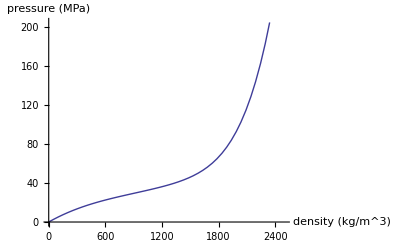

```mathematica
Plot[βp[ρ*ρCO2Conversion,σCO2,β290,ϵCO2]/(β290)*Pa2MPa,{ρ,ρmin, ρmax},AxesLabel->{"density (kg/m^3)","pressure (MPa)"}]
```

```mathematica
Export["Figures\\co2_ig_hs_assoc_disp_extended.jpg",Plot[βp[ρ*ρCO2Conversion,σCO2,β290,ϵCO2]/(β290)*Pa2MPa,{ρ,ρmin, ρmax},AxesLabel->{"density (kg/m^3)","pressure (MPa)"}]]
```

Figures\co2_ig_hs_assoc_disp_extended.jpg

Right order of magnitude. Wrong curvature.

## 2. Numerical Solving

## 3. Sanity Checks (thermodynamic relations)